```mathematica
ClearAll["Global`*"]
```

## AA 279 - PS 2 - Ellipsoids

#### Saving

```mathematica
NotebookDirectory[]
title="ps3_axial";
savename[specific_]:=StringJoin[NotebookDirectory[],"figures\\",title,"_",specific,".png"]

savename["test"]
```

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_test.png

### Ellipsoids

```mathematica
energyEllipsoidAxes[t_,imom_]:=2 t/imom
momentumEllipsoidAxes[l_,imom_]:=l^2/imom^2

(*omega1 = {0.0873,0.0698,0.0524}, bound = 0.2*)
(*omega2 = 3 * omega1, bound = 3*0.2*)
(*omega3 = 5*{-0.0099,0.99995,-0.00004}, bound = 9*)
(*omega4 = 5*{0, 1, 0}, bound = 9*)

omegabounds=0.2
omegainital=Quantity[{0.0873,0.0698,0.0524},1/("Seconds")];
(*isat=Quantity[{4770.398,6313.894,7413.202},"Kilograms" ("Meters")^2];*)
(*isat=Quantity[{4770.398,6313.894,7413.202},"Kilograms" ("Meters")^2];*)
isat=Quantity[{4770.398,4770.398,7413.202},"Kilograms" ("Meters")^2]
lvecstart=isat*omegainital;
lstart=Norm[lvecstart]

tstart=1/2 lvecstart.omegainital

(*tstart=Quantity[43.7365,"Joules"];
lstart=Quantity[720.1078,("Kilogram"*("Meters")^2)/("Seconds")];*)

energyaxes=UnitConvert[√energyEllipsoidAxes[tstart,isat]]
momentumaxes=UnitConvert[√momentumEllipsoidAxes[lstart,isat]]
```

0.2

{4770.4 kg m^2,4770.4 kg m^2,7413.2 kg m^2}

659.698 kg m^2/s

39.9765 kg m^2/s^2

{0.129461 per second,0.129461 per second,0.103852 per second}

{0.13829 per second,0.13829 per second,0.0889896 per second}

```mathematica
Graphics3D[{{Orange,Specularity[White,10],Opacity[0.6],Ellipsoid[{0,0,0},QuantityMagnitude[energyaxes]]},
{Cyan,Specularity[White,10],Opacity[0.6],Ellipsoid[{0,0,0},QuantityMagnitude[momentumaxes]]}}
]
```

-Graphics3D-

```mathematica
ωvec={ωx,ωy,ωz};
ωvecunits=Quantity[ωvec,1/("Seconds")];
energyeq=(ωvecunits^2).(1/energyaxes^2)
momentumeq=(ωvecunits^2).(1/momentumaxes^2)
```

59.665 ωx^2+59.665 ωy^2+92.7195 ωz^2

52.29 ωx^2+52.29 ωy^2+126.276 ωz^2

```mathematica
(*energyeq-momentumeq

Solve[{energyeq-momentumeq==0,energyeq==1,momentumeq==1},ωvec]*)
```

```mathematica
noPolhodeContourPlot=ContourPlot3D[{energyeq==1,momentumeq==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},Mesh->None,ContourStyle->Opacity[0.8],PlotTheme->"Detailed",AxesLabel->{"ω_x","ω_y","ω_z"},MaxRecursion->3,PlotPoints->120,AxesStyle->Black]
Export[savename["ellipsoids_no_polhode"],noPolhodeContourPlot,ImageResolution->300]

polhodeContourPlot=ContourPlot3D[{energyeq==1,momentumeq==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},MeshFunctions->{Function[{ωx,ωy,ωz,f},energyeq-momentumeq]},MeshStyle->{{Thick,Black}},Mesh->{{0}},ContourStyle->Opacity[0.8],PlotTheme->"Detailed",AxesLabel->{"ω_x","ω_y","ω_z"},MaxRecursion->3,PlotPoints->60,AxesStyle->Black]
Export[savename["ellipsoids_with_polhode"],polhodeContourPlot,ImageResolution->300]
```

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_ellipsoids_no_polhode.png

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_ellipsoids_with_polhode.png

#### Solve Euler Equations

```mathematica
eulerode={
ωx'[t]==1/ix((iy-iz)ωy[t]ωz[t]-mx),
ωy'[t]==1/iy((iz-ix)ωx[t]ωz[t]-my),
ωz'[t]==1/iz((ix-iy)ωx[t]ωy[t]-mz)};
eulerodeparams=eulerode/.{mx->0,my->0,mz->0,ix->isat[[1]],iy->isat[[2]],iz->isat[[3]]};

starttime=0.0;
endtime=360.0;
initconds={
ωx[starttime]==QuantityMagnitude[omegainital[[1]]],
ωy[starttime]==QuantityMagnitude[omegainital[[2]]],
ωz[starttime]==QuantityMagnitude[omegainital[[3]]]}

fulleulerivp=Flatten[{eulerodeparams,initconds}]

eulersol=NDSolve[fulleulerivp,{ωx,ωy,ωz},{t,starttime,endtime}]

numericalsolplot=Plot[Evaluate[{ωx[t],ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},AxesLabel->{"Time [s]","ω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"ω_x","ω_y","ω_z"}]

Export[savename["numerical_integration"],numericalsolplot,ImageResolution->300]
```

{ωx[0.]==0.0873,ωy[0.]==0.0698,ωz[0.]==0.0524}

{ωx'[t]==-0.554001 ωy[t] ωz[t],ωy'[t]==0.554001 ωx[t] ωz[t],ωz'[t]==0.,ωx[0.]==0.0873,ωy[0.]==0.0698,ωz[0.]==0.0524}

{{ωx→InterpolatingFunction[…],ωy→InterpolatingFunction[…],ωz→InterpolatingFunction[…]}}

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_numerical_integration.png

```mathematica
polhodeParametric=ParametricPlot3D[Evaluate[{ωx[t],ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]

contourwithcalcpolhode=Show[noPolhodeContourPlot,polhodeParametric]

Export[savename["ellipsoids_with_calculated_polhode"],contourwithcalcpolhode,ImageResolution->300]
```

-Graphics3D-

-Graphics3D-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_ellipsoids_with_calculated_polhode.png

### Analytical solution (I_x=I_y≠I_z)

```mathematica
amat = ({{0, -λ}, {λ, 0}})
amat.amat//MatrixForm
MatrixExp[amat]//MatrixForm
Eigensystem[amat]
```

{{0,-λ},{λ,0}}

(-λ^2 | 0
0 | -λ^2)

(Cos[λ] | -Sin[λ]
Sin[λ] | Cos[λ])

{{ⅈ λ,-ⅈ λ},{{ⅈ,1},{-ⅈ,1}}}

```mathematica
umat=1/(√2)({{ⅈ, -ⅈ}, {1, 1}});
umat//MatrixForm
Inverse[umat]//MatrixForm
ConjugateTranspose[umat]//MatrixForm
```

(ⅈ/(√2) | -ⅈ/(√2)
1/(√2) | 1/(√2))

(-ⅈ/(√2) | 1/(√2)
ⅈ/(√2) | 1/(√2))

(-ⅈ/(√2) | 1/(√2)
ⅈ/(√2) | 1/(√2))

```mathematica
dmat=({{ⅈ λ, 0}, {0, -ⅈ λ}});
umat.dmat.ConjugateTranspose[umat]//MatrixForm
```

(0 | -λ
λ | 0)

```mathematica
dmat=({{ⅈ λ, 0}, {0, -ⅈ λ}});
umat.MatrixExp[dmat].ConjugateTranspose[umat]//MatrixForm
FullSimplify[umat.MatrixExp[dmat].ConjugateTranspose[umat]]//MatrixForm
```

(ⅇ^(-ⅈ λ)/2+ⅇ^(ⅈ λ)/2 | -1/2 ⅈ ⅇ^(-ⅈ λ)+1/2 ⅈ ⅇ^(ⅈ λ)
1/2 ⅈ ⅇ^(-ⅈ λ)-1/2 ⅈ ⅇ^(ⅈ λ) | ⅇ^(-ⅈ λ)/2+ⅇ^(ⅈ λ)/2)

(Cos[λ] | -Sin[λ]
Sin[λ] | Cos[λ])

```mathematica
λcurr=(isat[[3]]/isat[[1]]-1)omegainital[[3]]
ωxAnalytical[t_]:=Cos[λcurr t]omegainital[[1]]-Sin[λcurr t]omegainital[[2]]
ωyAnalytical[t_]:=Sin[λcurr t]omegainital[[1]]+Cos[λcurr t]omegainital[[2]]

ωxAnalyticalNoUnits[t_]:=QuantityMagnitude[ωxAnalytical[Quantity[t,"Seconds"]]]
ωyAnalyticalNoUnits[t_]:=QuantityMagnitude[ωyAnalytical[Quantity[t,"Seconds"]]]
ωzAnalyticalNoUnits[t_]:=QuantityMagnitude[omegainital[[3]]]

analyticalsolplot=Plot[{ωxAnalyticalNoUnits[t],ωyAnalyticalNoUnits[t],ωzAnalyticalNoUnits[t]},{t,starttime,endtime},AxesLabel->{"Time [s]","ω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"ω_x","ω_y","ω_z"}]

Export[savename["analytical_integration"],analyticalsolplot,ImageResolution->300]
```

0.0290296 per second

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_analytical_integration.png

```mathematica
diffFunc[analytical_,numerical_,sol_,t_]:=analytical[t]-Evaluate[numerical[t]/.sol]

diffplot=Plot[{
diffFunc[ωxAnalyticalNoUnits,ωx,eulersol,t],
diffFunc[ωyAnalyticalNoUnits,ωy,eulersol,t],
diffFunc[ωzAnalyticalNoUnits,ωz,eulersol,t]},
{t,starttime,endtime},FrameLabel->{"Time [s]","Δω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"Δω_x","Δω_y","Δω_z"},PlotTheme->"Detailed",PlotLegends->{"Δω_x","Δω_y","Δω_z"}]

Export[savename["integration_difference"],diffplot,ImageResolution->300]
```

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_integration_difference.png

```mathematica
diffplotlongtime=Plot[{
diffFunc[ωxAnalyticalNoUnits,ωx,eulersol,t],
diffFunc[ωyAnalyticalNoUnits,ωy,eulersol,t],
diffFunc[ωzAnalyticalNoUnits,ωz,eulersol,t]},
{t,starttime,2*endtime},FrameLabel->{"Time [s]","Δω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"Δω_x","Δω_y","Δω_z"},PlotTheme->"Detailed",PlotLegends->{"Δω_x","Δω_y","Δω_z"},PlotRange->All]

Export[savename["integration_difference_long_time"],diffplotlongtime,ImageResolution->300]
```

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_integration_difference_long_time.png

### Bad Solution

```mathematica
eulersolbadsol=NDSolve[fulleulerivp,{ωx,ωy,ωz},{t,starttime,10*endtime},Method->{"TimeIntegration"->{"Extrapolation"}}]

numericalsolbadsolplot=Plot[Evaluate[{ωx[t],ωy[t],ωz[t]}/.eulersolbadsol],{t,starttime,10*endtime},AxesLabel->{"Time [s]","ω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"ω_x","ω_y","ω_z"}]

(*Export[savename["numerical_integration_badsol"],numericalsolplot,ImageResolution->300]*)
```

{{ωx→InterpolatingFunction[…],ωy→InterpolatingFunction[…],ωz→InterpolatingFunction[…]}}

-Graphics-

```mathematica
diffplotbad=Plot[{
diffFunc[ωxAnalyticalNoUnits,ωx,eulersolbadsol,t],
diffFunc[ωyAnalyticalNoUnits,ωy,eulersolbadsol,t],
diffFunc[ωzAnalyticalNoUnits,ωz,eulersolbadsol,t]},
{t,starttime,endtime},FrameLabel->{"Time [s]","Δω [rad/s]"},AxesStyle->Black,FrameStyle->Black,PlotLabels->{"Δω_x","Δω_y","Δω_z"},PlotTheme->"Detailed",PlotLegends->{"Δω_x","Δω_y","Δω_z"},PlotRange->All]

Export[savename["integration_difference_bad"],diffplotbad,ImageResolution->300]
```

-Graphics-

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_integration_difference_bad.png

### 2D Projection Plots

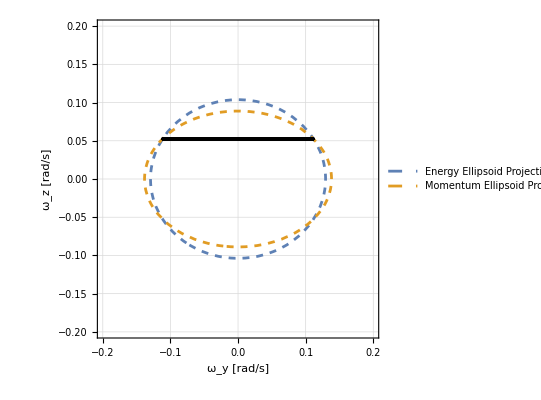

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_projected_polhode_yz.png

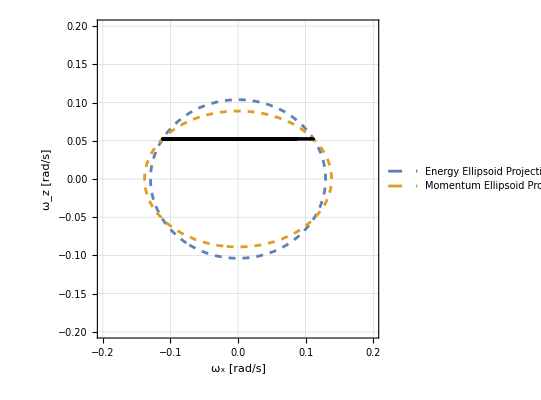

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_projected_polhode_xz.png

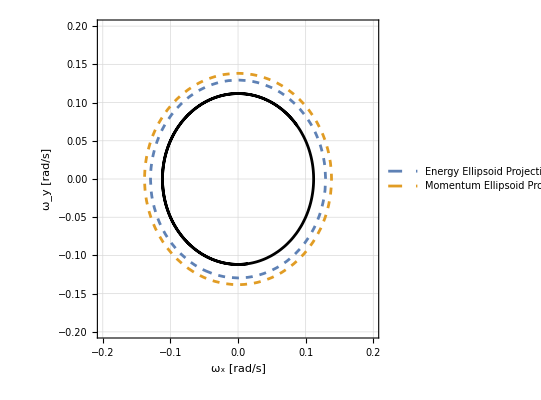

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_projected_polhode_xy.png

```mathematica
yz2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωx->0]==1,Evaluate[momentumeq/.ωx->0]==1},{ωy,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_y [rad/s]","ω_z [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωy[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]
]
Export[savename["projected_polhode_yz"],yz2dproj,ImageResolution->300]

xz2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωy->0]==1,Evaluate[momentumeq/.ωy->0]==1},{ωx,-omegabounds,omegabounds},{ωz,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_x [rad/s]","ω_z [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωx[t],ωz[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black]
]
Export[savename["projected_polhode_xz"],xz2dproj,ImageResolution->300]

xy2dproj=Show[
ContourPlot[{Evaluate[energyeq/.ωz->0]==1,Evaluate[momentumeq/.ωz->0]==1},{ωx,-omegabounds,omegabounds},{ωy,-omegabounds,omegabounds},ContourStyle->Dashed,FrameLabel->{"ω_x [rad/s]","ω_y [rad/s]"},PlotTheme->"Detailed",GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->{"Energy Ellipsoid Projection","Momentum Ellipsoid Projection"},FrameStyle->Black],
ParametricPlot[Evaluate[{ωx[t],ωy[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black,PlotLabel->Automatic]
]
Export[savename["projected_polhode_xy"],xy2dproj,ImageResolution->300]
```

### Non-Dimensionalized

```mathematica
bΠ1=isat[[3]] Norm[omegainital]^2/tstart
bΠ2=isat[[3]] Norm[omegainital]/lstart

bΠ1prime=lstart^2/(2tstart isat[[3]])
bΠ2prime=(lstart Norm[omegainital])/tstart

ihatx=isat[[1]]/isat[[3]]
ihaty=isat[[2]]/isat[[3]]
```

2.82592

1.3872

0.73426

2.03714

0.6435

0.6435

0.324144 hatωx^2+0.324144 hatωy^2

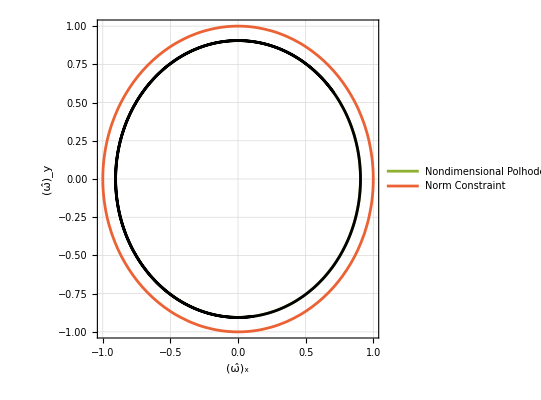

C:\Users\Daniel N\Desktop\GitHub\AA279C\ps2_mathematica\figures\ps3_axial_nondim_polhode.png

```mathematica
nondimellipseterm[ihat_,b1πp_]:=(1-b1πp-(ihat-b1πp)ihat)

nondimeq=nondimellipseterm[ihatx,bΠ1prime] hatωx^2+nondimellipseterm[ihaty,bΠ1prime] hatωy^2

nondimpolhode=Show[
ContourPlot[{0==0,0==0,nondimeq==1-bΠ1prime,hatωx^2+hatωy^2==1},{hatωx,-1,1},{hatωy,-1,1},PlotTheme->"Detailed",FrameLabel->{"(ω̂)_x","(ω̂)_y"},PlotLegends->{None,None,"Nondimensional Polhode","Norm Constraint"},GridLines->Automatic,GridLinesStyle->Dotted,FrameStyle->Black],
ParametricPlot[Evaluate[1/Norm[{ωx[t],ωy[t],ωz[t]}]{ωx[t],ωy[t]}/.eulersol],{t,starttime,endtime},PlotStyle->Black,PlotLabel->Automatic]
]

Export[savename["nondim_polhode"],nondimpolhode,ImageResolution->300]
```